## Definitions

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(* Harper antiperiodic *)
hharpa[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*antiperiodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_]:=hharp[Fibonacci[n-2],Fibonacci[n-1]];
hfiba[n_]:=hharpa[Fibonacci[n-2],Fibonacci[n-1]];
```

## Typical x, typical eigenfunction

Let us note Ω^n(x) the number of states having a given value of x at step n. One has
Ω^n(x) = Ω(n_m,n_a) with n_m=n x the number of molecular renormalizations, and n_a=n (1-2x)/3 the number of atomic renormalizations, and
Ω(p,q)=2^p((p+q)!)/(p! q!).
When n becomes large, we have Log(Ω^n(x)) ~ f(x) Log(F_n) ~ n Log(ϕ)×f(x) with Log(ϕ)×f(x) = -x Log(3x/2) + (1+x)/3Log(1+x) - (1 - 2x)/3Log(1-2x)
The Log erases a constant factor N. To recover it we simply note that N F_n^(f(x)-1) should be the probability density of x. Thus by the steepest descent method we get
N = √((n σ)/(2 π)) with σ = Log(ϕ) |f''(x_0)|.
The final thing to do to compare asymptotic result for the probability density with Ω^n/F_n is to take the continuous limit. Since there are approximately n/3 values of x at step n, we simply multiply by n/3.

```mathematica
f[x_]:= (-x Log[3x/2] + (1+x)/3 Log[1+x] - (1 - 2x)/3 Log[1-2x])/Log[ω^-1];
```

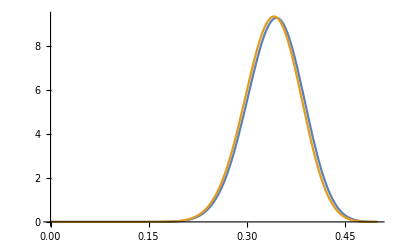

```mathematica
step=80;
(* number of states having value x when n = step *)
compt[x_]:=2^(step x)((step (1+x)/3)!)/((step x)!(step (1-2x)/3)!);
(* exact probability density of x *)
exactfreq[x_]:=step/3 compt[x]/Fibonacci[step];
(* compute variance *)
x0=2(3ω-1)/5; (* this is the value of x that makes f stationnary *)
σ=-f''[x0]*Log[ω^-1];
(* asymptotic probability density of x *)
freq[x_]:=√((step σ)/(2 π))Fibonacci[step]^(f[x]-1);
Plot[{exactfreq[x],freq[x]},{x,0,1/2},PlotRange->All]
```

So, the typical value of x is x_0 such that
f'(x_0) = 0

```mathematica
Solve[f'[x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.341641}}

x_0=2(1-ω^4)/5=2(1-2+3ω)/5=2(3ω-1)/5
We have f(x_0)=1

## Typical exponent

### Definitions

In the large size limit, almost all wavefunctions have x=x_0. Therefore they have the exponent τ_q(x_0). We also compute the average exponent
χ_q=1/F_n Σ_a χ_q(a) = 1/F_n Σ_x Ω(x) χ_q(x).
Thus, we obtain that the average exponent is the exponent of the typical wavefunction:
τ_q=τ_q(x_0)+1-f(x_0) = τ_q(x_0).

This is perhaps too crude a reasoning, since we neglect completely the variance of the probability density of x. More rigorously we write
χ_q = N∫dx F_n^(f(x)-1)F_n^(-τ_q(x))
We let g(x) = - log(ϕ)(f(x)-1) ~ σ/2(x-x_0)^2
and t_q × x = log(ϕ) τ_q(x). (At leading order in ρ τ is linear in x. At second order it is affine in x).
Then [computation to be checked]
χ_q~ e^(-n(t x_0-σt^2/2)) and thus
τ_q=τ_q(x_0)-(σ t_q^2)/(2 log(ϕ))

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBands[n_,ρ_]:=IntBands[n,ρ]=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqInt[q_,n_,ρ_]:=avqInt[q,n,ρ]=Total[IntBands[n,ρ][[1]]^q,2]/Fibonacci[n];
```

We expect Log (χ^n)_q ~ -τ_q Log F_n , and indeed, Log (χ^n)_q is a linear function of n ~ Log F_n:

### Tests

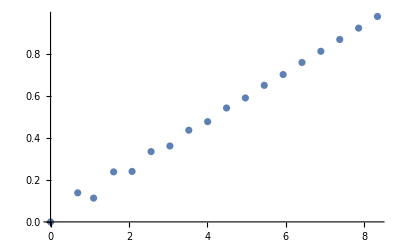

```mathematica
nValues=Range[2,19,1];
avIntN=Map[avqInt[.8,#,0.1]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

For large values of q, the 3-periodic behaviour of the Fibonacci numbers (odd, odd, even...) is clearly visible.
It turns out that when F_n is even, there is a gap at E=0, while there is a band when F_n is odd. Since there is an energy level at E=0 for the quasicrystalline chain, we guess that choosing odd approximant is a better idea. If F_n is odd and F_(n-2) as well, then the 2 lateral clusters have also a band in their center. This is perhaps even better.

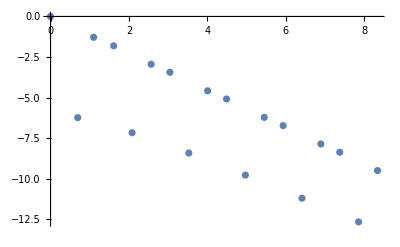

```mathematica
nValues=Range[2,19,1];
avIntN=Map[avqInt[10.,#,0.1]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

For q into the range [0,1) it is safe to disregard the 3-periodicity dependance. Below we compute the slope ie -τ_q for n=13, 16, 19 for different values of q between 0 and 1.

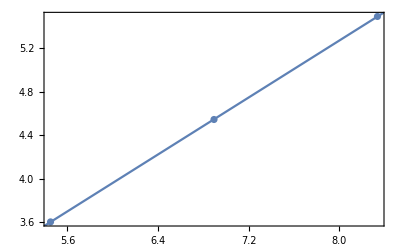

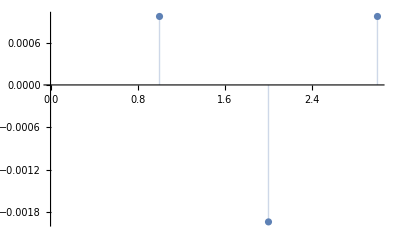

```mathematica
qValues=Range[0,0.9,0.05];
nValues={13,16,19};
avIntN=Map[avqInt[0.2,#,0.1]&,nValues];

dat=glue[Log[Fibonacci[nValues]],Log[avIntN]];
fit=LinearModelFit[dat,n,n];
Show[ListPlot[dat],Plot[fit[n],{n,0,10}],Frame->True]
ListPlot[fit["FitResiduals"], Filling->Axis]
```

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
fits=linFit[#,0.1,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqs=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q] *)
dqs=MapThread[#1/(#2-1)&,{tauqs,qValues}];
(* convert to Subscript[Δ, q] *)
Δqs=MapThread[(#1-(#2-1))&,{tauqs,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

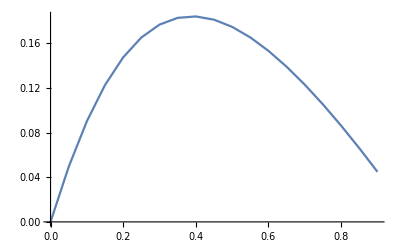

```mathematica
ListPlot[glue[qValues,Δqs],Joined->True]
```

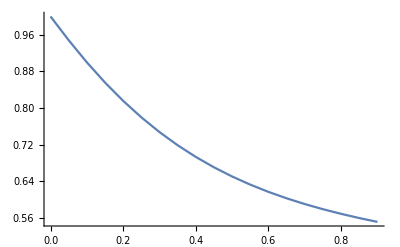

```mathematica
ListPlot[glue[qValues,dqs],Joined->True]
```

### Comparison analytical results

It is also possible to derive recursion relations on χ_q^n using the second-order perturbation theory on wavefunctions:
χ_q^n=2(λ/2)^q ω^2 χ_q^(n-2)+(λ')^q ω^3 χ_q^(n-3)
with λ = 1/(1+ρ^2/2), λ'=1/(1+2 ρ^2).

Using that χ_q~F_n^-τ_q, we arrive at an implicit equation on τ_q:

```mathematica
ω=(√5-1)/2//N;
```

```mathematica
gam[ρ_,q_]:=1/(1+ρ^q);
lambp[ρ_]:=((1+gam[ρ,1.] ρ^2-√(1+(gam[ρ,1.] ρ^2)^2))/(2gam[ρ,1.] ρ^2))^-1;
barlambp[ρ_]:=((√((1+ρ^2)^4+4 ρ^4)-(1+ρ^2)^2)/(2 ρ^4))^-1;
```

```mathematica
Cm[q_,τq_,ρ_]:=(2+(3-2ω)gam[ρ,q] ρ^(2q))ω^(-2τq)+gam[ρ,q] ρ^(2q)(ω^3/barlambp[ρ]^q ω^(-5τq)-(4 ω^2)/lambp[ρ]^q ω^(-4τq));
Ca[q_,τq_,ρ_]:=(1+2 ρ^(2q)+(3-2ω)ρ^(4q))ω^(-3τq)+ρ^(4q)(ω^3/barlambp[ρ]^q ω^(-6τq)-(4 ω^2)/lambp[ρ]^q ω^(-5τq));
eq[q_,τq_,ρ_]:=(2 ω^2)/lambp[ρ]^q Cm[q,τq,ρ]+ω^3/barlambp[ρ]^q Ca[q,τq,ρ]-1;
```

```mathematica
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,0.}]
```

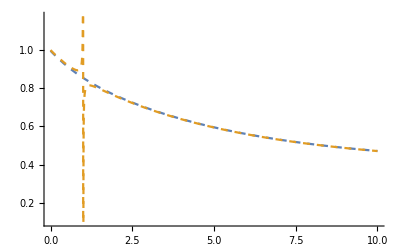

```mathematica
(* heal the divergency by substracting Subscript[τ, 1]≃ 10^-2 *)
Block[{ρ=.5},Plot[{(implicitTau[q,ρ]-implicitTau[1,ρ])/(q-1),implicitTau[q,ρ]/(q-1)},{q,0,10.},PlotStyle->Dashed]]
```

For q into the range [0,20] we compute the slope ie -τ_q using the points n=13, 16, 19.

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
nValues={13,16,19};
fits=linFit[#,.8,nValues]&/@qValues;
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqs=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q] *)
dqs=MapThread[#1/(#2-1)&,{tauqs,qValues}];
(* convert to Subscript[Δ, q] *)
Δqs=MapThread[(#1-(#2-1))&,{tauqs,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

```mathematica
(* export τ as a function of q for a given ρ to data file *)
(*Export[NotebookDirectory[]<>"data/tauqpsi_rho_08.dat",glue[qValues,tauqs]];*)
```

```mathematica
(* import τ as a function of q *)
τq05=Import[NotebookDirectory[]<>"data/tauqpsi_rho_05.dat"];
τq1=Import[NotebookDirectory[]<>"data/tauqpsi_rho_1.dat"];
τq09=Import[NotebookDirectory[]<>"data/tauqpsi_rho_09.dat"];
τq02=Import[NotebookDirectory[]<>"data/tauqpsi_rho_02.dat"];
τq03=Import[NotebookDirectory[]<>"data/tauqpsi_rho_03.dat"];
τq04=Import[NotebookDirectory[]<>"data/tauqpsi_rho_04.dat"];
τq06=Import[NotebookDirectory[]<>"data/tauqpsi_rho_06.dat"];
```

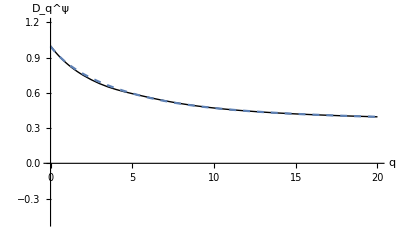

```mathematica
dq05=MapThread[{#1,#2/(#1-1)}&,Transpose[τq05]];
Plot[(implicitTau[q,0.5]-implicitTau[1,0.5])/(q-1),{q,0.,20.},Prolog->{Thick,Line@dq05},PlotRange->{{0.,20},{-0.5,1.2}},AxesLabel->{"q","D_q^ψ"},PlotStyle->Dashed]
```

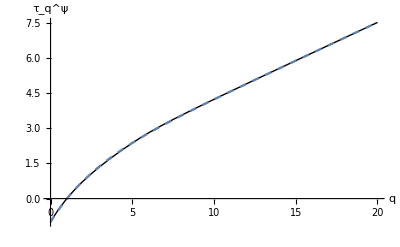

```mathematica
Plot[{implicitTau[q,.5]},{q,0.,20.},Prolog->{Thick,Line@τq05},PlotRange->All,AxesLabel->{"q","τ_q^ψ"},PlotStyle->Dashed]
```

The 3-periodicity is also visible (although much less apparent) for the Harper model using the golden ratio as the irrational (see subsection below).

## Improved numerics

### Tests

```mathematica
(* IntBands returns intensities averaged over p and anti-p boundary conditions *)
ρ=0.1;
int13=IntBands[13,ρ][[1]];
```

```mathematica
(* export intensity list to avoid computing it again *)
Export[NotebookDirectory[]<>"int19.dat",int19];
```

```mathematica
(* we clearly have lost precision of the smallest coefficients *)
Max[int19]/Min[int19]
```

3.72312×10^31

```mathematica
(* where are these low precision sites? *)
threshold=10^-12;
M=Max[int13];
belowpos13=Position[int13,int_/;int≤M*threshold];
```

```mathematica
belowar13=SparseArray[belowpos13->1,{Fibonacci[13],Fibonacci[13]}];
MatrixPlot[belowar13,ColorFunction->"Monochrome",MaxPlotPoints->Infinity]
```

-Graphics-

```mathematica
(* where are these low precision sites? *)
threshold=10^-12;
M=Max[int19];
belowpos19=Position[int19,int_/;int≤M*threshold];
```

```mathematica
belowar19=SparseArray[belowpos19->1,{Fibonacci[19],Fibonacci[19]}];
MatrixPlot[belowar19,ColorFunction->"Monochrome",MaxPlotPoints->Infinity]
```

-Graphics-

### Sample the α distribution directly

α = Log(|ψ|^2)/Log(1/F_n)

```mathematica
α13=Log[int13]/Log[1/Fibonacci[13]];
```

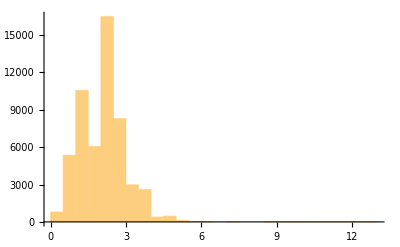

```mathematica
Histogram[Flatten[α13]]
```

```mathematica
α19=Log[int19]/Log[1/Fibonacci[19]];
```

```mathematica
αmin=0.2;
αmax=2.3;
Δα=0.08;
```

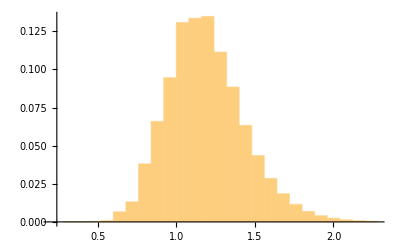

```mathematica
hist=Histogram[Flatten[α19],{αmin,αmax,Δα},"Probability"]
```

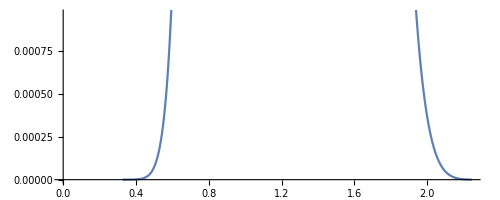

```mathematica
pthexp=ParametricPlot[{fα05th[[1]],Fibonacci[19]^(fα05th[[2]]-1)*0.15},{q,-10,20}]
```

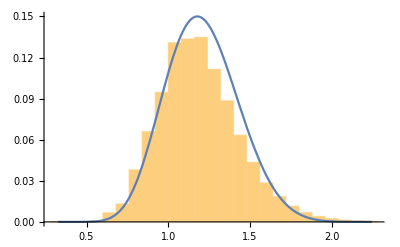

```mathematica
Show[hist,pthexp,PlotRange->All]
```

```mathematica
𝒟α=HistogramDistribution[Flatten[α19],{αmin,αmax,Δα}]
```

DataDistribution[…]

```mathematica
psampled=DiscretePlot[Log@(PDF[𝒟α,x])/Log@Fibonacci[19]+1-0.07,{x,0.2,2.4,Δα},PlotRange->All];
```

```mathematica
pth=ParametricPlot[fα05th,{q,-10,20}];
```

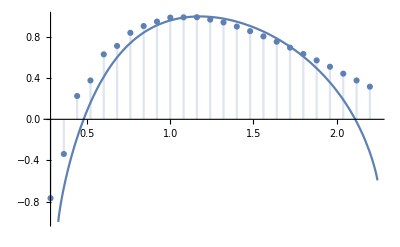

```mathematica
Show[psampled,pth,PlotRange->All]
```

### Bunching

Regroup sites by bunchs, to avoid numerical errors.

```mathematica
(* 4181 = 37*113 *)
Divisors@Fibonacci[19]
```

{1,37,113,4181}

```mathematica
(* for each energy, average over clusters of 37 sites *)
(* for each energy, partition the wavefunction into clusters of 37 sites  *)
part19=Partition[#,37]&/@int19;
(* for each energy, perform the average over each cluster *)
av19=Mean[Transpose[#]]&/@part19;
```

```mathematica
avα19=Log[av19]/Log[1/Fibonacci[19]];
```

```mathematica
αmin=0.2;
αmax=2.3;
Δα=0.08;
```

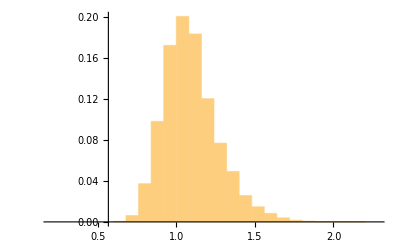

```mathematica
hist=Histogram[Flatten[avα19],{αmin,αmax,Δα},"Probability"]
```

### Remove low precision sites from the intensity list

```mathematica
(* IntBands returns intensities averaged over p and anti-p boundary conditions *)
ρ=0.1;
int13=IntBands[13,ρ][[1]];
```

```mathematica
int15=IntBands[15,ρ][[1]];
```

```mathematica
int19=Import[NotebookDirectory[]<>"temp/int19.dat"];
```

```mathematica
(* return the intensity list intlist with all terms below M*threshold deleted *)
delete[intlist_,threshold_]:=Block[{M=Max[intlist],below},
below=Position[intlist,int_/;int≤M*threshold];
Delete[intlist,below]
]
```

```mathematica
threshold=10^-10;
```

```mathematica
del13=delete[int13,threshold];
```

```mathematica
del15=delete[int15,threshold];
```

```mathematica
del19=delete[int19,threshold];
```

```mathematica
(* compute the average intensity from the new intensity list *)
avIntDel[q_,int_]:=Total[int^q,2]/Length[int];
```

```mathematica
delints={Length[#],avIntDel[-0.5,#]}&/@{del13,del15,del19}
```

{{233,530571.},{610,3.29835×10^6},{4181,1.23405×10^6}}

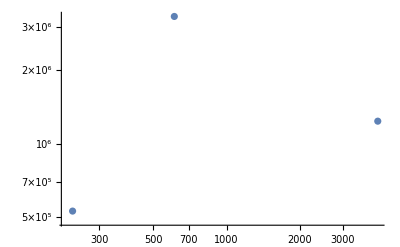

```mathematica
ListLogLogPlot[delints]
```

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

## Harper model

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBandsHarp[n_]:=IntBandsHarp[n]=Block[{vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n]];
{vpa,wfa}=Eigensystem[hfiba[n]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqIntHarp[q_,n_]:=avqIntHarp[q,n]=Total[IntBandsHarp[n][[1]]^q,2]/Fibonacci[n];
```

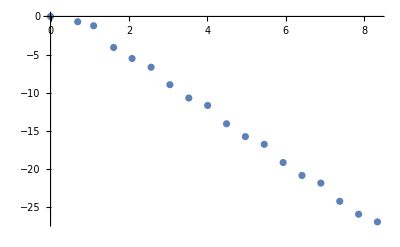

```mathematica
nValues=Range[2,19,1];
avIntN=ParallelMap[avqIntHarp[15.,#]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

For q into the range [0,20] we compute the slope ie -τ_q using the points n=10, 13, 16, 19.

```mathematica
linFitHarp[q_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqIntHarp[q,#]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
qValuesHarp=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
nValuesHarp={10,13,16,19};
fitsHarp=linFitHarp[#,nValuesHarp]&/@qValuesHarp;
```

$Aborted

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqsHarp=-Normal[#["ParameterTable"]][[1,3,2]]&/@fitsHarp;
(* convert to Subscript[D, q] *)
dqsHarp=MapThread[#1/(#2-1)&,{tauqsHarp,qValuesHarp}];
```

Part::partd: Part specification linFitHarp[0., 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

Part::partd: Part specification linFitHarp[0.05, 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

Part::partd: Part specification linFitHarp[0.1, 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

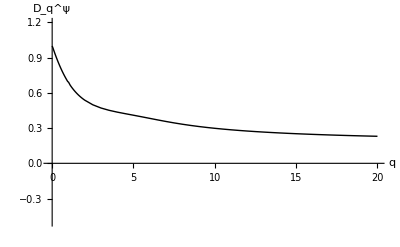

```mathematica
Plot[{},{q,1.1,20.},Prolog->{Thick,Line@glue[qValuesHarp,dqsHarp]},PlotRange->{{-0.1,20},{-0.5,1.2}},AxesLabel->{"q","D_q^ψ"},PlotStyle->Dashed]
```

```mathematica
Export[NotebookDirectory[]<>"../Harper/data/average_wf_dimension.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/../Harper/data/average_wf_dimension.pdf